# Minimal binding network for slope antagonism

Here we analyze possible binding networks given in the following picture-

We first perform calculation for the general network A using- -Graphics-

The dynamical equations are-

```mathematica
dadt=Subscript[k, a0]+Subscript[P, 1]*Subscript[k, 1]*Subscript[s, 1]+Subscript[P, 4]*Subscript[k, 4]*Subscript[s, 2]-Subscript[k, da]*a-γ*a*b
dbdt=Subscript[k, b0]+Subscript[P, 3]*Subscript[k, 3]*Subscript[s, 1]+Subscript[P, 2]*Subscript[k, 2]*Subscript[s, 2]-Subscript[k, db]*b-γ*a*b
Solve[{dadt==0,dbdt==0},{a,b}]
```

-a b γ+k_a0-a k_da+k_1 P_1 s_1+k_4 P_4 s_2

-a b γ+k_b0-b k_db+k_3 P_3 s_1+k_2 P_2 s_2

{{a→1/(2 γ k_da)(γ k_a0-γ k_b0-k_da k_db+γ k_1 P_1 s_1-γ k_3 P_3 s_1-γ k_2 P_2 s_2+γ k_4 P_4 s_2-√((-γ k_a0+γ k_b0+k_da k_db-γ k_1 P_1 s_1+γ k_3 P_3 s_1+γ k_2 P_2 s_2-γ k_4 P_4 s_2)^2-4 γ k_da (-k_a0 k_db-k_1 k_db P_1 s_1-k_4 k_db P_4 s_2))),b→1/k_db(-k_a0/2+k_b0/2-(k_da k_db)/(2 γ)-1/2 k_1 P_1 s_1+1/2 k_3 P_3 s_1+1/2 k_2 P_2 s_2-1/2 k_4 P_4 s_2-(√((-γ k_a0+γ k_b0+k_da k_db-γ k_1 P_1 s_1+γ k_3 P_3 s_1+γ k_2 P_2 s_2-γ k_4 P_4 s_2)^2-4 γ k_da (-k_a0 k_db-k_1 k_db P_1 s_1-k_4 k_db P_4 s_2)))/(2 γ))},{a→1/(2 γ k_da)(γ k_a0-γ k_b0-k_da k_db+γ k_1 P_1 s_1-γ k_3 P_3 s_1-γ k_2 P_2 s_2+γ k_4 P_4 s_2+√((-γ k_a0+γ k_b0+k_da k_db-γ k_1 P_1 s_1+γ k_3 P_3 s_1+γ k_2 P_2 s_2-γ k_4 P_4 s_2)^2-4 γ k_da (-k_a0 k_db-k_1 k_db P_1 s_1-k_4 k_db P_4 s_2))),b→1/k_db(-k_a0/2+k_b0/2-(k_da k_db)/(2 γ)-1/2 k_1 P_1 s_1+1/2 k_3 P_3 s_1+1/2 k_2 P_2 s_2-1/2 k_4 P_4 s_2+(√((-γ k_a0+γ k_b0+k_da k_db-γ k_1 P_1 s_1+γ k_3 P_3 s_1+γ k_2 P_2 s_2-γ k_4 P_4 s_2)^2-4 γ k_da (-k_a0 k_db-k_1 k_db P_1 s_1-k_4 k_db P_4 s_2)))/(2 γ))}}

Accounting for the positivity of a and b we can write the steady state expressions for a and b as,

```mathematica
aSS=FullSimplify[1/(2 γ Subscript[k, da])(γ Subscript[k, a0]-γ Subscript[k, b0]-Subscript[k, da] Subscript[k, db]+γ Subscript[k, 1] Subscript[P, 1] Subscript[s, 1]-γ Subscript[k, 3] Subscript[P, 3] Subscript[s, 1]-γ Subscript[k, 2] Subscript[P, 2] Subscript[s, 2]+γ Subscript[k, 4] Subscript[P, 4] Subscript[s, 2]+√((-γ Subscript[k, a0]+γ Subscript[k, b0]+Subscript[k, da] Subscript[k, db]-γ Subscript[k, 1] Subscript[P, 1] Subscript[s, 1]+γ Subscript[k, 3] Subscript[P, 3] Subscript[s, 1]+γ Subscript[k, 2] Subscript[P, 2] Subscript[s, 2]-γ Subscript[k, 4] Subscript[P, 4] Subscript[s, 2])^2-4 γ Subscript[k, da] (-Subscript[k, a0] Subscript[k, db]-Subscript[k, 1] Subscript[k, db] Subscript[P, 1] Subscript[s, 1]-Subscript[k, 4] Subscript[k, db] Subscript[P, 4] Subscript[s, 2])))]
```

1/(2 γ k_da)(-k_da k_db+γ (k_a0-k_b0+(k_1 P_1-k_3 P_3) s_1+(-k_2 P_2+k_4 P_4) s_2)+√(4 γ k_da k_db (k_a0+k_1 P_1 s_1+k_4 P_4 s_2)+(k_da k_db+γ (-k_a0+k_b0+(-k_1 P_1+k_3 P_3) s_1+(k_2 P_2-k_4 P_4) s_2))^2))

```mathematica
bSS=FullSimplify[1/Subscript[k, db](-Subscript[k, a0]/2+Subscript[k, b0]/2-(Subscript[k, da] Subscript[k, db])/(2 γ)-1/2 Subscript[k, 1] Subscript[P, 1] Subscript[s, 1]+1/2 Subscript[k, 3] Subscript[P, 3] Subscript[s, 1]+1/2 Subscript[k, 2] Subscript[P, 2] Subscript[s, 2]-1/2 Subscript[k, 4] Subscript[P, 4] Subscript[s, 2]+(√((-γ Subscript[k, a0]+γ Subscript[k, b0]+Subscript[k, da] Subscript[k, db]-γ Subscript[k, 1] Subscript[P, 1] Subscript[s, 1]+γ Subscript[k, 3] Subscript[P, 3] Subscript[s, 1]+γ Subscript[k, 2] Subscript[P, 2] Subscript[s, 2]-γ Subscript[k, 4] Subscript[P, 4] Subscript[s, 2])^2-4 γ Subscript[k, da] (-Subscript[k, a0] Subscript[k, db]-Subscript[k, 1] Subscript[k, db] Subscript[P, 1] Subscript[s, 1]-Subscript[k, 4] Subscript[k, db] Subscript[P, 4] Subscript[s, 2])))/(2 γ))]
```

1/(2 γ k_db)(-k_da k_db+γ (-k_a0+k_b0+(-k_1 P_1+k_3 P_3) s_1+(k_2 P_2-k_4 P_4) s_2)+√(4 γ k_da k_db (k_a0+k_1 P_1 s_1+k_4 P_4 s_2)+(k_da k_db+γ (-k_a0+k_b0+(-k_1 P_1+k_3 P_3) s_1+(k_2 P_2-k_4 P_4) s_2))^2))

The expression for c in steady state is,

```mathematica
cSS=FullSimplify[γ*aSS*bSS/Subscript[k, dc]]
```

1/(2 γ k_dc)(k_da k_db+γ (k_a0+k_b0+(k_1 P_1+k_3 P_3) s_1+(k_2 P_2+k_4 P_4) s_2)-√(4 γ k_da k_db (k_a0+k_1 P_1 s_1+k_4 P_4 s_2)+(k_da k_db+γ (-k_a0+k_b0+(-k_1 P_1+k_3 P_3) s_1+(k_2 P_2-k_4 P_4) s_2))^2))

And finally the steady state expressions for m is-

```mathematica
mSS=FullSimplify[(Subscript[k, m0]+Subscript[P, 5]*Subscript[k, 5]*aSS+Subscript[P, 6]*Subscript[k, 6]*cSS+Subscript[P, 7]*Subscript[k, 7]*bSS)/Subscript[k, dm]]
```

1/(2 k_dm)(2 k_m0+1/(γ k_dc)k_6 P_6 (k_da k_db+γ (k_a0+k_b0+(k_1 P_1+k_3 P_3) s_1+(k_2 P_2+k_4 P_4) s_2)-√(4 γ k_da k_db (k_a0+k_1 P_1 s_1+k_4 P_4 s_2)+(k_da k_db+γ (-k_a0+k_b0+(-k_1 P_1+k_3 P_3) s_1+(k_2 P_2-k_4 P_4) s_2))^2))+1/(γ k_db)k_7 P_7 (-k_da k_db+γ (-k_a0+k_b0+(-k_1 P_1+k_3 P_3) s_1+(k_2 P_2-k_4 P_4) s_2)+√(4 γ k_da k_db (k_a0+k_1 P_1 s_1+k_4 P_4 s_2)+(k_da k_db+γ (-k_a0+k_b0+(-k_1 P_1+k_3 P_3) s_1+(k_2 P_2-k_4 P_4) s_2))^2))+1/(γ k_da)k_5 P_5 (-k_da k_db+γ (k_a0-k_b0+(k_1 P_1-k_3 P_3) s_1+(-k_2 P_2+k_4 P_4) s_2)+√(4 γ k_da k_db (k_a0+k_1 P_1 s_1+k_4 P_4 s_2)+(k_da k_db+γ (-k_a0+k_b0+(-k_1 P_1+k_3 P_3) s_1+(k_2 P_2-k_4 P_4) s_2))^2)))

### Now we set all reaction rates to 1 and determine the expressions for a,b,c and m in steady state for further analysis-

```mathematica
dadt=1+Subscript[P, 1]*1*Subscript[s, 1]+Subscript[P, 4]*1*Subscript[s, 2]-1*a-1*a*b
dbdt=1+Subscript[P, 3]*1*Subscript[s, 1]+Subscript[P, 2]*1*Subscript[s, 2]-1*b-1*a*b
Solve[{dadt==0,dbdt==0},{a,b}]
```

1-a-a b+P_1 s_1+P_4 s_2

1-b-a b+P_3 s_1+P_2 s_2

{{a→1/2 (-1+P_1 s_1-P_3 s_1-P_2 s_2+P_4 s_2-√(-4 (-1-P_1 s_1-P_4 s_2)+(1-P_1 s_1+P_3 s_1+P_2 s_2-P_4 s_2)^2)),b→1/2 (-1-P_1 s_1+P_3 s_1+P_2 s_2-P_4 s_2-√(-4 (-1-P_1 s_1-P_4 s_2)+(1-P_1 s_1+P_3 s_1+P_2 s_2-P_4 s_2)^2))},{a→1/2 (-1+P_1 s_1-P_3 s_1-P_2 s_2+P_4 s_2+√(-4 (-1-P_1 s_1-P_4 s_2)+(1-P_1 s_1+P_3 s_1+P_2 s_2-P_4 s_2)^2)),b→1/2 (-1-P_1 s_1+P_3 s_1+P_2 s_2-P_4 s_2+√(-4 (-1-P_1 s_1-P_4 s_2)+(1-P_1 s_1+P_3 s_1+P_2 s_2-P_4 s_2)^2))}}

```mathematica
{{a->1/2 (-1+Subscript[P, 1] Subscript[s, 1]-Subscript[P, 3] Subscript[s, 1]-Subscript[P, 2] Subscript[s, 2]+Subscript[P, 4] Subscript[s, 2]-√(-4 (-1-Subscript[P, 1] Subscript[s, 1]-Subscript[P, 4] Subscript[s, 2])+(1-Subscript[P, 1] Subscript[s, 1]+Subscript[P, 3] Subscript[s, 1]+Subscript[P, 2] Subscript[s, 2]-Subscript[P, 4] Subscript[s, 2])^2)),b->1/2 (-1-Subscript[P, 1] Subscript[s, 1]+Subscript[P, 3] Subscript[s, 1]+Subscript[P, 2] Subscript[s, 2]-Subscript[P, 4] Subscript[s, 2]-√(-4 (-1-Subscript[P, 1] Subscript[s, 1]-Subscript[P, 4] Subscript[s, 2])+(1-Subscript[P, 1] Subscript[s, 1]+Subscript[P, 3] Subscript[s, 1]+Subscript[P, 2] Subscript[s, 2]-Subscript[P, 4] Subscript[s, 2])^2))},{a->1/2 (-1+Subscript[P, 1] Subscript[s, 1]-Subscript[P, 3] Subscript[s, 1]-Subscript[P, 2] Subscript[s, 2]+Subscript[P, 4] Subscript[s, 2]+√(-4 (-1-Subscript[P, 1] Subscript[s, 1]-Subscript[P, 4] Subscript[s, 2])+(1-Subscript[P, 1] Subscript[s, 1]+Subscript[P, 3] Subscript[s, 1]+Subscript[P, 2] Subscript[s, 2]-Subscript[P, 4] Subscript[s, 2])^2)),b->1/2 (-1-Subscript[P, 1] Subscript[s, 1]+Subscript[P, 3] Subscript[s, 1]+Subscript[P, 2] Subscript[s, 2]-Subscript[P, 4] Subscript[s, 2]+√(-4 (-1-Subscript[P, 1] Subscript[s, 1]-Subscript[P, 4] Subscript[s, 2])+(1-Subscript[P, 1] Subscript[s, 1]+Subscript[P, 3] Subscript[s, 1]+Subscript[P, 2] Subscript[s, 2]-Subscript[P, 4] Subscript[s, 2])^2))}}
```

The steady state expressions are,

```mathematica
aP=FullSimplify[1/2 (-1+Subscript[P, 1] Subscript[s, 1]-Subscript[P, 3] Subscript[s, 1]-Subscript[P, 2] Subscript[s, 2]+Subscript[P, 4] Subscript[s, 2]+√(-4 (-1-Subscript[P, 1] Subscript[s, 1]-Subscript[P, 4] Subscript[s, 2])+(1-Subscript[P, 1] Subscript[s, 1]+Subscript[P, 3] Subscript[s, 1]+Subscript[P, 2] Subscript[s, 2]-Subscript[P, 4] Subscript[s, 2])^2))]
```

1/2 (-1+P_1 s_1-P_3 s_1-P_2 s_2+P_4 s_2+√((1+(-P_1+P_3) s_1+(P_2-P_4) s_2)^2+4 (1+P_1 s_1+P_4 s_2)))

```mathematica
bP=FullSimplify[1/2 (-1-Subscript[P, 1] Subscript[s, 1]+Subscript[P, 3] Subscript[s, 1]+Subscript[P, 2] Subscript[s, 2]-Subscript[P, 4] Subscript[s, 2]+√(-4 (-1-Subscript[P, 1] Subscript[s, 1]-Subscript[P, 4] Subscript[s, 2])+(1-Subscript[P, 1] Subscript[s, 1]+Subscript[P, 3] Subscript[s, 1]+Subscript[P, 2] Subscript[s, 2]-Subscript[P, 4] Subscript[s, 2])^2))]
```

1/2 (-1-P_1 s_1+P_3 s_1+P_2 s_2-P_4 s_2+√((1+(-P_1+P_3) s_1+(P_2-P_4) s_2)^2+4 (1+P_1 s_1+P_4 s_2)))

The steady state expressions for c is,

```mathematica
cP=FullSimplify[aP*bP]
```

1/2 (3+P_1 s_1+P_3 s_1+P_2 s_2+P_4 s_2-√((1+(-P_1+P_3) s_1+(P_2-P_4) s_2)^2+4 (1+P_1 s_1+P_4 s_2)))

And, finally the expression for the output m-

```mathematica
mP=FullSimplify[1+Subscript[P, 5]*1*aP+Subscript[P, 6]*1*cP+Subscript[P, 7]*1*bP]
```

1/2 (2+P_6 (3+P_1 s_1+P_3 s_1+P_2 s_2+P_4 s_2-√((1+(-P_1+P_3) s_1+(P_2-P_4) s_2)^2+4 (1+P_1 s_1+P_4 s_2)))+P_7 (-1-P_1 s_1+P_3 s_1+P_2 s_2-P_4 s_2+√((1+(-P_1+P_3) s_1+(P_2-P_4) s_2)^2+4 (1+P_1 s_1+P_4 s_2)))+P_5 (-1+P_1 s_1-P_3 s_1-P_2 s_2+P_4 s_2+√((1+(-P_1+P_3) s_1+(P_2-P_4) s_2)^2+4 (1+P_1 s_1+P_4 s_2))))

Expression for m only when one input is present,

```mathematica
mP1=FullSimplify[mP/.Subscript[s, 2]->0]
```

1/2 (2+P_6 (3+P_1 s_1+P_3 s_1-√(4+4 P_1 s_1+(1+(-P_1+P_3) s_1)^2))+P_5 (-1+P_1 s_1-P_3 s_1+√(4+4 P_1 s_1+(1+(-P_1+P_3) s_1)^2))+P_7 (-1-P_1 s_1+P_3 s_1+√(4+4 P_1 s_1+(1+(-P_1+P_3) s_1)^2)))

```mathematica
mP2=FullSimplify[mP/.Subscript[s, 1]->0]
```

1/2 (2+3 P_6-P_7+P_2 (P_6+P_7) s_2-(P_6-P_7) (-P_4 s_2+√(5+2 (P_2+P_4) s_2+(P_2-P_4)^2 s_2^2))+P_5 (-1+(-P_2+P_4) s_2+√(5+2 (P_2+P_4) s_2+(P_2-P_4)^2 s_2^2)))

Derivatives

```mathematica
Subscript[m, 1]=FullSimplify[D[mP1,Subscript[s, 1]]]
```

1/2 (P_6 (P_1+P_3+(-P_1-P_3-(P_1-P_3)^2 s_1)/(√(4+4 P_1 s_1+(1+(-P_1+P_3) s_1)^2)))+P_5 (P_1-P_3+(P_1+P_3+(P_1-P_3)^2 s_1)/(√(4+4 P_1 s_1+(1+(-P_1+P_3) s_1)^2)))+P_7 (-P_1+P_3+(P_1+P_3+(P_1-P_3)^2 s_1)/(√(4+4 P_1 s_1+(1+(-P_1+P_3) s_1)^2))))

```mathematica
Subscript[m, 2]=FullSimplify[D[mP2,Subscript[s, 2]]]
```

1/2 (P_2 (P_6+P_7)-(P_6-P_7) (-P_4+(P_2+P_4+(P_2-P_4)^2 s_2)/(√(5+2 (P_2+P_4) s_2+(P_2-P_4)^2 s_2^2)))+P_5 (-P_2+P_4+(P_2+P_4+(P_2-P_4)^2 s_2)/(√(5+2 (P_2+P_4) s_2+(P_2-P_4)^2 s_2^2))))

```mathematica
Subscript[m, 12]=FullSimplify[D[mP,Subscript[s, 1]]+D[mP,Subscript[s, 2]]]
```

1/2 (P_6 (P_1+P_3-(4 P_1+2 (-P_1+P_3) (1+(-P_1+P_3) s_1+(P_2-P_4) s_2))/(2 √((1+(-P_1+P_3) s_1+(P_2-P_4) s_2)^2+4 (1+P_1 s_1+P_4 s_2))))+P_5 (P_1-P_3+(4 P_1+2 (-P_1+P_3) (1+(-P_1+P_3) s_1+(P_2-P_4) s_2))/(2 √((1+(-P_1+P_3) s_1+(P_2-P_4) s_2)^2+4 (1+P_1 s_1+P_4 s_2))))+P_7 (-P_1+P_3+(4 P_1+2 (-P_1+P_3) (1+(-P_1+P_3) s_1+(P_2-P_4) s_2))/(2 √((1+(-P_1+P_3) s_1+(P_2-P_4) s_2)^2+4 (1+P_1 s_1+P_4 s_2))))+P_6 (P_2+P_4-(4 P_4+2 (P_2-P_4) (1+(-P_1+P_3) s_1+(P_2-P_4) s_2))/(2 √((1+(-P_1+P_3) s_1+(P_2-P_4) s_2)^2+4 (1+P_1 s_1+P_4 s_2))))+P_7 (P_2-P_4+(4 P_4+2 (P_2-P_4) (1+(-P_1+P_3) s_1+(P_2-P_4) s_2))/(2 √((1+(-P_1+P_3) s_1+(P_2-P_4) s_2)^2+4 (1+P_1 s_1+P_4 s_2))))+P_5 (-P_2+P_4+(4 P_4+2 (P_2-P_4) (1+(-P_1+P_3) s_1+(P_2-P_4) s_2))/(2 √((1+(-P_1+P_3) s_1+(P_2-P_4) s_2)^2+4 (1+P_1 s_1+P_4 s_2)))))

## Surface maps for networks B,C,D

## Network B

```mathematica
Subscript[P, 1]=1;
Subscript[P, 2]=1;
Subscript[P, 3]=1;
Subscript[P, 4]=1;
Subscript[P, 5]=1;
Subscript[P, 6]=1;
Subscript[P, 7]=1;
mPB=1/2 (2+Subscript[P, 6] (3+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 3] Subscript[s, 1]+Subscript[P, 2] Subscript[s, 2]+Subscript[P, 4] Subscript[s, 2]-√((1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2])^2+4 (1+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 4] Subscript[s, 2])))+Subscript[P, 7] (-1-Subscript[P, 1] Subscript[s, 1]+Subscript[P, 3] Subscript[s, 1]+Subscript[P, 2] Subscript[s, 2]-Subscript[P, 4] Subscript[s, 2]+√((1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2])^2+4 (1+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 4] Subscript[s, 2])))+Subscript[P, 5] (-1+Subscript[P, 1] Subscript[s, 1]-Subscript[P, 3] Subscript[s, 1]-Subscript[P, 2] Subscript[s, 2]+Subscript[P, 4] Subscript[s, 2]+√((1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2])^2+4 (1+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 4] Subscript[s, 2]))))
```

1/2 (3+2 s_1+2 s_2+√(1+4 (1+s_1+s_2)))

```mathematica
Plot3D[mPB,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["m(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["m(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15],ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

## Network C

```mathematica
Subscript[P, 1]=1;
Subscript[P, 2]=1;
Subscript[P, 3]=0;
Subscript[P, 4]=0;
Subscript[P, 5]=1;
Subscript[P, 6]=1;
Subscript[P, 7]=1;
mPC=1/2 (2+Subscript[P, 6] (3+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 3] Subscript[s, 1]+Subscript[P, 2] Subscript[s, 2]+Subscript[P, 4] Subscript[s, 2]-√((1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2])^2+4 (1+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 4] Subscript[s, 2])))+Subscript[P, 7] (-1-Subscript[P, 1] Subscript[s, 1]+Subscript[P, 3] Subscript[s, 1]+Subscript[P, 2] Subscript[s, 2]-Subscript[P, 4] Subscript[s, 2]+√((1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2])^2+4 (1+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 4] Subscript[s, 2])))+Subscript[P, 5] (-1+Subscript[P, 1] Subscript[s, 1]-Subscript[P, 3] Subscript[s, 1]-Subscript[P, 2] Subscript[s, 2]+Subscript[P, 4] Subscript[s, 2]+√((1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2])^2+4 (1+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 4] Subscript[s, 2]))))
```

1/2 (3+s_1+s_2+√(4 (1+s_1)+(1-s_1+s_2)^2))

```mathematica
Plot3D[mPC,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["m(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["m(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15],ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

## Network D

```mathematica
Subscript[P, 1]=1;
Subscript[P, 2]=1;
Subscript[P, 3]=0;
Subscript[P, 4]=1;
Subscript[P, 5]=1;
Subscript[P, 6]=1;
Subscript[P, 7]=0;
mPD=1/2 (2+Subscript[P, 6] (3+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 3] Subscript[s, 1]+Subscript[P, 2] Subscript[s, 2]+Subscript[P, 4] Subscript[s, 2]-√((1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2])^2+4 (1+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 4] Subscript[s, 2])))+Subscript[P, 7] (-1-Subscript[P, 1] Subscript[s, 1]+Subscript[P, 3] Subscript[s, 1]+Subscript[P, 2] Subscript[s, 2]-Subscript[P, 4] Subscript[s, 2]+√((1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2])^2+4 (1+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 4] Subscript[s, 2])))+Subscript[P, 5] (-1+Subscript[P, 1] Subscript[s, 1]-Subscript[P, 3] Subscript[s, 1]-Subscript[P, 2] Subscript[s, 2]+Subscript[P, 4] Subscript[s, 2]+√((1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2])^2+4 (1+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 4] Subscript[s, 2]))))
```

1/2 (4+2 s_1+2 s_2)

```mathematica
Plot3D[mPD,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["m(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["m(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15],ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

## Successful network value antagonism

## This is the code to test the successful network for value antagonism -

```mathematica
npts=10000; (*number of random {Subscript[s, 1],Subscript[s, 2]} pairs over which the antagonism condition is verified*)
smax=100; (*maximum value of Subscript[s, 1] and Subscript[s, 2]*)
nedges=7; (*maximum number of edges*)
Print["Successful binding networks for value antagonism-\n"]
For[i=0,i<2^nedges,i++,Subscript[P, 1]=PadLeft[IntegerDigits[i,2],nedges][[1]];Subscript[P, 2]=PadLeft[IntegerDigits[i,2],nedges][[2]];Subscript[P, 3]=PadLeft[IntegerDigits[i,2],nedges][[3]];
Subscript[P, 4]=PadLeft[IntegerDigits[i,2],nedges][[4]];
Subscript[P, 5]=PadLeft[IntegerDigits[i,2],nedges][[5]];
Subscript[P, 6]=PadLeft[IntegerDigits[i,2],nedges][[6]];
Subscript[P, 7]=PadLeft[IntegerDigits[i,2],nedges][[7]];
For[j=0,j<npts,j++,Subscript[s, 1]=smax*RandomReal[];
Subscript[s, 2]=smax*RandomReal[];
mP=1/2 (2+Subscript[P, 6] (3+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 3] Subscript[s, 1]+Subscript[P, 2] Subscript[s, 2]+Subscript[P, 4] Subscript[s, 2]-√((1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2])^2+4 (1+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 4] Subscript[s, 2])))+Subscript[P, 7] (-1-Subscript[P, 1] Subscript[s, 1]+Subscript[P, 3] Subscript[s, 1]+Subscript[P, 2] Subscript[s, 2]-Subscript[P, 4] Subscript[s, 2]+√((1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2])^2+4 (1+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 4] Subscript[s, 2])))+Subscript[P, 5] (-1+Subscript[P, 1] Subscript[s, 1]-Subscript[P, 3] Subscript[s, 1]-Subscript[P, 2] Subscript[s, 2]+Subscript[P, 4] Subscript[s, 2]+√((1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2])^2+4 (1+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 4] Subscript[s, 2]))));
m00=1/2 (2+(-1+√5) Subscript[P, 5]-(-3+√5) Subscript[P, 6]+(-1+√5) Subscript[P, 7]);mP1=1/2 (2+Subscript[P, 6] (3+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 3] Subscript[s, 1]-√(4+4 Subscript[P, 1] Subscript[s, 1]+(1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1])^2))+Subscript[P, 5] (-1+Subscript[P, 1] Subscript[s, 1]-Subscript[P, 3] Subscript[s, 1]+√(4+4 Subscript[P, 1] Subscript[s, 1]+(1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1])^2))+Subscript[P, 7] (-1-Subscript[P, 1] Subscript[s, 1]+Subscript[P, 3] Subscript[s, 1]+√(4+4 Subscript[P, 1] Subscript[s, 1]+(1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1])^2)));mP2=1/2 (2+3 Subscript[P, 6]-Subscript[P, 7]+Subscript[P, 2] (Subscript[P, 6]+Subscript[P, 7]) Subscript[s, 2]-(Subscript[P, 6]-Subscript[P, 7]) (-Subscript[P, 4] Subscript[s, 2]+√(5+2 (Subscript[P, 2]+Subscript[P, 4]) Subscript[s, 2]+(Subscript[P, 2]-Subscript[P, 4])^2 Subscript[s, 2]^2))+Subscript[P, 5] (-1+(-Subscript[P, 2]+Subscript[P, 4]) Subscript[s, 2]+√(5+2 (Subscript[P, 2]+Subscript[P, 4]) Subscript[s, 2]+(Subscript[P, 2]-Subscript[P, 4])^2 Subscript[s, 2]^2)));If[mP1>m00&&mP2>m00&&mP<Min[mP1,mP2],Print["P_1=",Subscript[P, 1],", P_2=",Subscript[P, 2],", P_3=",Subscript[P, 3],", P_4=",Subscript[P, 4],", P_5=",Subscript[P, 5],", P_6=",Subscript[P, 6],", P_7=",Subscript[P, 7],", Total edges=",Total[IntegerDigits[i,2]]]&&Break[],0]]]
```

Successful binding networks for value antagonism-

P_1=0, P_2=0, P_3=1, P_4=1, P_5=1, P_6=0, P_7=1, Total edges=4

P_1=1, P_2=1, P_3=0, P_4=0, P_5=1, P_6=0, P_7=1, Total edges=4

This is the surface map for the successful network-

```mathematica
Subscript[P, 1]=1;
Subscript[P, 2]=1;
Subscript[P, 3]=0;
Subscript[P, 4]=0;
Subscript[P, 5]=1;
Subscript[P, 6]=0;
Subscript[P, 7]=1;
mPSV=1/2 (2+Subscript[P, 6] (3+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 3] Subscript[s, 1]+Subscript[P, 2] Subscript[s, 2]+Subscript[P, 4] Subscript[s, 2]-√((1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2])^2+4 (1+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 4] Subscript[s, 2])))+Subscript[P, 7] (-1-Subscript[P, 1] Subscript[s, 1]+Subscript[P, 3] Subscript[s, 1]+Subscript[P, 2] Subscript[s, 2]-Subscript[P, 4] Subscript[s, 2]+√((1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2])^2+4 (1+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 4] Subscript[s, 2])))+Subscript[P, 5] (-1+Subscript[P, 1] Subscript[s, 1]-Subscript[P, 3] Subscript[s, 1]-Subscript[P, 2] Subscript[s, 2]+Subscript[P, 4] Subscript[s, 2]+√((1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2])^2+4 (1+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 4] Subscript[s, 2]))))
```

√(4 (1+s_1)+(1-s_1+s_2)^2)

```mathematica
Plot3D[mPSV,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["m(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["m(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15],ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

## Successful network slope antagonism

## This is the code to test the successful network for slope antagonism-

```mathematica
npts=10000; (*number of random {Subscript[s, 1],Subscript[s, 2]} pairs over which the antagonism condition is verified*)
smax=100; (*maximum value of Subscript[s, 1] and Subscript[s, 2]*)
nedges=7; (*maximum number of edges*)
Print["Successful binding networks for slope antagonism-\n"]
For[i=0,i<2^nedges,i++,Subscript[P, 1]=PadLeft[IntegerDigits[i,2],nedges][[1]];Subscript[P, 2]=PadLeft[IntegerDigits[i,2],nedges][[2]];Subscript[P, 3]=PadLeft[IntegerDigits[i,2],nedges][[3]];
Subscript[P, 4]=PadLeft[IntegerDigits[i,2],nedges][[4]];
Subscript[P, 5]=PadLeft[IntegerDigits[i,2],nedges][[5]];
Subscript[P, 6]=PadLeft[IntegerDigits[i,2],nedges][[6]];
Subscript[P, 7]=PadLeft[IntegerDigits[i,2],nedges][[7]];
For[j=0,j<npts,j++,Subscript[s, 1]=smax*RandomReal[];
Subscript[s, 2]=smax*RandomReal[];
Subscript[m, 12]=1/2 (Subscript[P, 6] (Subscript[P, 1]+Subscript[P, 3]-(4 Subscript[P, 1]+2 (-Subscript[P, 1]+Subscript[P, 3]) (1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2]))/(2 √((1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2])^2+4 (1+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 4] Subscript[s, 2]))))+Subscript[P, 5] (Subscript[P, 1]-Subscript[P, 3]+(4 Subscript[P, 1]+2 (-Subscript[P, 1]+Subscript[P, 3]) (1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2]))/(2 √((1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2])^2+4 (1+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 4] Subscript[s, 2]))))+Subscript[P, 7] (-Subscript[P, 1]+Subscript[P, 3]+(4 Subscript[P, 1]+2 (-Subscript[P, 1]+Subscript[P, 3]) (1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2]))/(2 √((1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2])^2+4 (1+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 4] Subscript[s, 2]))))+Subscript[P, 6] (Subscript[P, 2]+Subscript[P, 4]-(4 Subscript[P, 4]+2 (Subscript[P, 2]-Subscript[P, 4]) (1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2]))/(2 √((1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2])^2+4 (1+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 4] Subscript[s, 2]))))+Subscript[P, 7] (Subscript[P, 2]-Subscript[P, 4]+(4 Subscript[P, 4]+2 (Subscript[P, 2]-Subscript[P, 4]) (1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2]))/(2 √((1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2])^2+4 (1+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 4] Subscript[s, 2]))))+Subscript[P, 5] (-Subscript[P, 2]+Subscript[P, 4]+(4 Subscript[P, 4]+2 (Subscript[P, 2]-Subscript[P, 4]) (1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2]))/(2 √((1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2])^2+4 (1+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 4] Subscript[s, 2])))));
Subscript[m, 00]=0;Subscript[m, 1]=1/2 (Subscript[P, 6] (Subscript[P, 1]+Subscript[P, 3]+(-Subscript[P, 1]-Subscript[P, 3]-(Subscript[P, 1]-Subscript[P, 3])^2 Subscript[s, 1])/(√(4+4 Subscript[P, 1] Subscript[s, 1]+(1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1])^2)))+Subscript[P, 5] (Subscript[P, 1]-Subscript[P, 3]+(Subscript[P, 1]+Subscript[P, 3]+(Subscript[P, 1]-Subscript[P, 3])^2 Subscript[s, 1])/(√(4+4 Subscript[P, 1] Subscript[s, 1]+(1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1])^2)))+Subscript[P, 7] (-Subscript[P, 1]+Subscript[P, 3]+(Subscript[P, 1]+Subscript[P, 3]+(Subscript[P, 1]-Subscript[P, 3])^2 Subscript[s, 1])/(√(4+4 Subscript[P, 1] Subscript[s, 1]+(1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1])^2))));Subscript[m, 2]=1/2 (Subscript[P, 2] (Subscript[P, 6]+Subscript[P, 7])-(Subscript[P, 6]-Subscript[P, 7]) (-Subscript[P, 4]+(Subscript[P, 2]+Subscript[P, 4]+(Subscript[P, 2]-Subscript[P, 4])^2 Subscript[s, 2])/(√(5+2 (Subscript[P, 2]+Subscript[P, 4]) Subscript[s, 2]+(Subscript[P, 2]-Subscript[P, 4])^2 Subscript[s, 2]^2)))+Subscript[P, 5] (-Subscript[P, 2]+Subscript[P, 4]+(Subscript[P, 2]+Subscript[P, 4]+(Subscript[P, 2]-Subscript[P, 4])^2 Subscript[s, 2])/(√(5+2 (Subscript[P, 2]+Subscript[P, 4]) Subscript[s, 2]+(Subscript[P, 2]-Subscript[P, 4])^2 Subscript[s, 2]^2))));If[Subscript[m, 1]>Subscript[m, 00]&&Subscript[m, 2]>Subscript[m, 00]&&Subscript[m, 12]<Min[Subscript[m, 1],Subscript[m, 2]],Print["P_1=",Subscript[P, 1],", P_2=",Subscript[P, 2],", P_3=",Subscript[P, 3],", P_4=",Subscript[P, 4],", P_5=",Subscript[P, 5],", P_6=",Subscript[P, 6],", P_7=",Subscript[P, 7],", Total edges=",Total[IntegerDigits[i,2]]]&&Break[],0]]]
```

Successful binding networks for slope antagonism-

P_1=0, P_2=0, P_3=1, P_4=1, P_5=1, P_6=0, P_7=1, Total edges=4

P_1=0, P_2=1, P_3=1, P_4=0, P_5=0, P_6=1, P_7=0, Total edges=3

P_1=1, P_2=0, P_3=0, P_4=1, P_5=0, P_6=1, P_7=0, Total edges=3

P_1=1, P_2=1, P_3=0, P_4=0, P_5=1, P_6=0, P_7=1, Total edges=4

```mathematica
Subscript[P, 1]=0;
Subscript[P, 2]=1;
Subscript[P, 3]=1;
Subscript[P, 4]=0;
Subscript[P, 5]=0;
Subscript[P, 6]=1;
Subscript[P, 7]=0;
mPSS=FullSimplify[1/2 (2+Subscript[P, 6] (3+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 3] Subscript[s, 1]+Subscript[P, 2] Subscript[s, 2]+Subscript[P, 4] Subscript[s, 2]-√((1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2])^2+4 (1+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 4] Subscript[s, 2])))+Subscript[P, 7] (-1-Subscript[P, 1] Subscript[s, 1]+Subscript[P, 3] Subscript[s, 1]+Subscript[P, 2] Subscript[s, 2]-Subscript[P, 4] Subscript[s, 2]+√((1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2])^2+4 (1+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 4] Subscript[s, 2])))+Subscript[P, 5] (-1+Subscript[P, 1] Subscript[s, 1]-Subscript[P, 3] Subscript[s, 1]-Subscript[P, 2] Subscript[s, 2]+Subscript[P, 4] Subscript[s, 2]+√((1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2])^2+4 (1+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 4] Subscript[s, 2]))))]
```

```mathematica
1/2 (5+Subscript[s, 1]+Subscript[s, 2]-√(4+(1+Subscript[s, 1]+Subscript[s, 2])^2))
```

```mathematica
Plot3D[mPSS,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["m(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["m(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15],ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

## Calculating m_1,m_2 and m_12 for succesful slope antagonism

```mathematica
Subscript[P, 1]=0;
Subscript[P, 2]=1;
Subscript[P, 3]=1;
Subscript[P, 4]=0;
Subscript[P, 5]=0;
Subscript[P, 6]=1;
Subscript[P, 7]=0;
Subscript[m, S1]=FullSimplify[1/2 (Subscript[P, 6] (Subscript[P, 1]+Subscript[P, 3]+(-Subscript[P, 1]-Subscript[P, 3]-(Subscript[P, 1]-Subscript[P, 3])^2 Subscript[s, 1])/(√(4+4 Subscript[P, 1] Subscript[s, 1]+(1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1])^2)))+Subscript[P, 5] (Subscript[P, 1]-Subscript[P, 3]+(Subscript[P, 1]+Subscript[P, 3]+(Subscript[P, 1]-Subscript[P, 3])^2 Subscript[s, 1])/(√(4+4 Subscript[P, 1] Subscript[s, 1]+(1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1])^2)))+Subscript[P, 7] (-Subscript[P, 1]+Subscript[P, 3]+(Subscript[P, 1]+Subscript[P, 3]+(Subscript[P, 1]-Subscript[P, 3])^2 Subscript[s, 1])/(√(4+4 Subscript[P, 1] Subscript[s, 1]+(1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1])^2))))]
```

1/2 (1+(-1-s_1)/(√(4+(1+s_1)^2)))

```mathematica
Subscript[P, 1]=0;
Subscript[P, 2]=1;
Subscript[P, 3]=1;
Subscript[P, 4]=0;
Subscript[P, 5]=0;
Subscript[P, 6]=1;
Subscript[P, 7]=0;
Subscript[m, S2]=FullSimplify[1/2 (Subscript[P, 2] (Subscript[P, 6]+Subscript[P, 7])-(Subscript[P, 6]-Subscript[P, 7]) (-Subscript[P, 4]+(Subscript[P, 2]+Subscript[P, 4]+(Subscript[P, 2]-Subscript[P, 4])^2 Subscript[s, 2])/(√(5+2 (Subscript[P, 2]+Subscript[P, 4]) Subscript[s, 2]+(Subscript[P, 2]-Subscript[P, 4])^2 Subscript[s, 2]^2)))+Subscript[P, 5] (-Subscript[P, 2]+Subscript[P, 4]+(Subscript[P, 2]+Subscript[P, 4]+(Subscript[P, 2]-Subscript[P, 4])^2 Subscript[s, 2])/(√(5+2 (Subscript[P, 2]+Subscript[P, 4]) Subscript[s, 2]+(Subscript[P, 2]-Subscript[P, 4])^2 Subscript[s, 2]^2))))]
```

1/2 (1-(1+s_2)/(√(5+s_2 (2+s_2))))

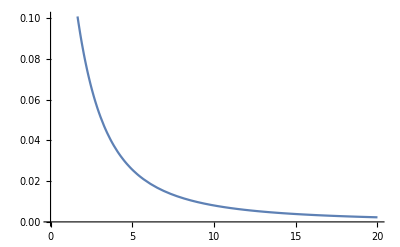

```mathematica
Plot[1/2 (1-(1+Subscript[s, 2])/(√(5+Subscript[s, 2] (2+Subscript[s, 2])))),{Subscript[s, 2],0,20}]
```

```mathematica
Subscript[P, 1]=0;
Subscript[P, 2]=1;
Subscript[P, 3]=1;
Subscript[P, 4]=0;
Subscript[P, 5]=0;
Subscript[P, 6]=1;
Subscript[P, 7]=0;
Subscript[m, S12]=FullSimplify[1/2 (Subscript[P, 6] (Subscript[P, 1]+Subscript[P, 3]-(4 Subscript[P, 1]+2 (-Subscript[P, 1]+Subscript[P, 3]) (1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2]))/(2 √((1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2])^2+4 (1+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 4] Subscript[s, 2]))))+Subscript[P, 5] (Subscript[P, 1]-Subscript[P, 3]+(4 Subscript[P, 1]+2 (-Subscript[P, 1]+Subscript[P, 3]) (1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2]))/(2 √((1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2])^2+4 (1+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 4] Subscript[s, 2]))))+Subscript[P, 7] (-Subscript[P, 1]+Subscript[P, 3]+(4 Subscript[P, 1]+2 (-Subscript[P, 1]+Subscript[P, 3]) (1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2]))/(2 √((1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2])^2+4 (1+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 4] Subscript[s, 2]))))+Subscript[P, 6] (Subscript[P, 2]+Subscript[P, 4]-(4 Subscript[P, 4]+2 (Subscript[P, 2]-Subscript[P, 4]) (1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2]))/(2 √((1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2])^2+4 (1+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 4] Subscript[s, 2]))))+Subscript[P, 7] (Subscript[P, 2]-Subscript[P, 4]+(4 Subscript[P, 4]+2 (Subscript[P, 2]-Subscript[P, 4]) (1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2]))/(2 √((1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2])^2+4 (1+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 4] Subscript[s, 2]))))+Subscript[P, 5] (-Subscript[P, 2]+Subscript[P, 4]+(4 Subscript[P, 4]+2 (Subscript[P, 2]-Subscript[P, 4]) (1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2]))/(2 √((1+(-Subscript[P, 1]+Subscript[P, 3]) Subscript[s, 1]+(Subscript[P, 2]-Subscript[P, 4]) Subscript[s, 2])^2+4 (1+Subscript[P, 1] Subscript[s, 1]+Subscript[P, 4] Subscript[s, 2])))))]
```

1-(1+s_1+s_2)/(√(4+(1+s_1+s_2)^2))